```mathematica
{{T2KNDwidth={.4,.3,.3,.5,.5,1,1,1};
baseT2KND={{0.2+0.001,10.3*10*T2KNDwidth[[1]]},{0.55,78.6*10*T2KNDwidth[[2]]},{0.85,44.2*10*T2KNDwidth[[3]]},{1.25,10.0*10*T2KNDwidth[[4]]},{1.75,3.73*10*T2KNDwidth[[5]]},{2.5,2.0*10*T2KNDwidth[[6]]},{3.5,1.15*10*T2KNDwidth[[7]]},{4.5,0.57*10*T2KNDwidth[[8]]}};
T2KND=Table[{x,1500PDF[CauchyDistribution[0.64,0.21],x]},{x,baseT2KND[[All,1]]}];
antiT2KND=Table[{x,300 PDF[CauchyDistribution[0.64,0.21],x]},{x,baseT2KND[[All,1]]}];

NOvANDwidth={0.75,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25};
baseNOvAND={{0.75/2+0.001,0.125},{1-.25/2,1.875},{1.25-.25/2,3.375},{1.5-.25/2,10.875},{1.75-.25/2,30.375},{2.0-.25/2,51.125},{2.25-.25/2,46.625},{2.5-.25/2,27.4375},{2.75-.25/2,13.9375},{3.0-.25/2,7.5625},{3.25-.25/2,4.3125},{3.5-.25/2,2.9375},{3.75-0.25/2,2.375},{4.0-.25/2,2.125},{4.25-.25/2,1.8125},{4.5-.25/2,1.5},{4.75-.25/2,1.5},{5.0-.25/2,1.4375}};
NOvAND=Table[{x,800PDF[CauchyDistribution[2,0.35],x]},{x,baseNOvAND[[All,1]]}];
antiNOvAND=Table[{x,250PDF[CauchyDistribution[2,0.35],x]},{x,baseNOvAND[[All,1]]}];}, {□}}
```

{{Null^8},{□}}

```mathematica
ParallelEvaluate[
P[a_,b_,ρ_,LKm_,KEGeV_,dm21_,dm31_,dm41_,θ34_,δ34_,θ24_,θ14_,δ14_,θ23_,θ13_,δ13_,θ12_]:=(

Clear[L,KE,R12,R13,R23,R14,R24,R34];

L=N[LKm (10^10/1.9733)];KE=N[KEGeV (10^9)];

R12={{Cos[θ12],Sin[θ12],0,0},{-Sin[θ12],Cos[θ12],0,0},{0,0,1,0},{0,0,0,1}};
R13={{Cos[θ13],0,Sin[θ13]Exp[-I δ13],0},{0,1,0,0},{-Sin[θ13]Exp[I δ13],0,Cos[θ13],0},{0,0,0,1}};
R23={{1,0,0,0},{0,Cos[θ23],Sin[θ23],0},{0,-Sin[θ23],Cos[θ23],0},{0,0,0,1}};
R14={{Cos[θ14],0,0,Sin[θ14]Exp[-I δ14]},{0,1,0,0},{0,0,1,0},{-Sin[θ14]Exp[I δ14],0,0,Cos[θ14]}};
R24={{1,0,0,0},{0,Cos[θ24],0,Sin[θ24]},{0,0,1,0},{0,-Sin[θ24],0,Cos[θ24]}};
R34={{1,0,0,0},{0,1,0,0},{0,0,Cos[θ34],Sin[θ34]Exp[-I δ34]},{0,0,-Sin[θ34]Exp[I δ34],Cos[θ34]}};

U=Chop[R34.R24.R14.R23.R13.R12];

HF=1/(2KE)(U.{{0,0,0,0},{0,dm21,0,0},{0,0,dm31,0},{0,0,0,dm41}}.ConjugateTranspose[U]+{{1.52*^-4(0.5)ρ KE/10^9,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1.52*^-4(0.5/2) ρ KE/10^9}});
HFbar=1/(2KE)(U.{{0,0,0,0},{0,dm21,0,0},{0,0,dm31,0},{0,0,0,dm41}}.ConjugateTranspose[U]-{{1.52*^-4(0.5)ρ KE/10^9,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1.52*^-4(0.5/2) ρ KE/10^9}});

U4M=Chop[Transpose[Eigenvectors[HF]]];
U4Mbar=Chop[Transpose[Eigenvectors[HFbar]]];

M=2 KE ConjugateTranspose[U4M].HF.U4M;
Mbar=2 KE ConjugateTranspose[U4Mbar].HFbar.U4Mbar;

 {Chop[Sum[Conjugate[U4M[[a,k]]]U4M[[b,k]]U4M[[a,j]]Conjugate[U4M[[b,j]]]Exp[-I (M[[k,k]]-M[[j,j]])L/(2KE)],{k,1,4},{j,1,4}]],
Chop[Sum[U4Mbar[[a,k]]Conjugate[U4Mbar[[b,k]]]Conjugate[U4Mbar[[a,j]]]U4Mbar[[b,j]]Exp[-I (Mbar[[k,k]]-Mbar[[j,j]])L/(2KE)],{k,1,4},{j,1,4}]]}

);
]

P[a_,b_,ρ_,LKm_,KEGeV_,dm21_,dm31_,dm41_,θ34_,δ34_,θ24_,θ14_,δ14_,θ23_,θ13_,δ13_,θ12_]:=(

Clear[L,KE,R12,R13,R23,R14,R24,R34];

L=N[LKm (10^10/1.9733)];KE=N[KEGeV (10^9)];

R12={{Cos[θ12],Sin[θ12],0,0},{-Sin[θ12],Cos[θ12],0,0},{0,0,1,0},{0,0,0,1}};
R13={{Cos[θ13],0,Sin[θ13]Exp[-I δ13],0},{0,1,0,0},{-Sin[θ13]Exp[I δ13],0,Cos[θ13],0},{0,0,0,1}};
R23={{1,0,0,0},{0,Cos[θ23],Sin[θ23],0},{0,-Sin[θ23],Cos[θ23],0},{0,0,0,1}};
R14={{Cos[θ14],0,0,Sin[θ14]Exp[-I δ14]},{0,1,0,0},{0,0,1,0},{-Sin[θ14]Exp[I δ14],0,0,Cos[θ14]}};
R24={{1,0,0,0},{0,Cos[θ24],0,Sin[θ24]},{0,0,1,0},{0,-Sin[θ24],0,Cos[θ24]}};
R34={{1,0,0,0},{0,1,0,0},{0,0,Cos[θ34],Sin[θ34]Exp[-I δ34]},{0,0,-Sin[θ34]Exp[I δ34],Cos[θ34]}};

U=Chop[R34.R24.R14.R23.R13.R12];

HF=1/(2KE)(U.{{0,0,0,0},{0,dm21,0,0},{0,0,dm31,0},{0,0,0,dm41}}.ConjugateTranspose[U]+{{1.52*^-4(0.5)ρ KE/10^9,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1.52*^-4(0.5/2) ρ KE/10^9}});
HFbar=1/(2KE)(U.{{0,0,0,0},{0,dm21,0,0},{0,0,dm31,0},{0,0,0,dm41}}.ConjugateTranspose[U]-{{1.52*^-4(0.5)ρ KE/10^9,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1.52*^-4(0.5/2) ρ KE/10^9}});

U4M=Chop[Transpose[Eigenvectors[HF]]];
U4Mbar=Chop[Transpose[Eigenvectors[HFbar]]];

M=2 KE ConjugateTranspose[U4M].HF.U4M;
Mbar=2 KE ConjugateTranspose[U4Mbar].HFbar.U4Mbar;

 {Chop[Sum[Conjugate[U4M[[a,k]]]U4M[[b,k]]U4M[[a,j]]Conjugate[U4M[[b,j]]]Exp[-I (M[[k,k]]-M[[j,j]])L/(2KE)],{k,1,4},{j,1,4}]],
Chop[Sum[U4Mbar[[a,k]]Conjugate[U4Mbar[[b,k]]]Conjugate[U4Mbar[[a,j]]]U4Mbar[[b,j]]Exp[-I (Mbar[[k,k]]-Mbar[[j,j]])L/(2KE)],{k,1,4},{j,1,4}]]}

);
```

{Null,Null,Null,Null}

```mathematica
ρ=2.8;LT2K=N[295];LNOvA=N[810];

dm21=7.42*^-5;dm31=2.41*^-3; dm41=0;

θ12=33.44 Degree; θ13=8.57 Degree; θ23=ArcSin[Sqrt[0.57]];
δ13=1.4Pi;
θ34=0;θ24=0;θ14=0;
δ34=0;δ14=0;

FDT2Kμ=T2KND[[;;,2]]Table[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θ24,θ14,δ14,θ23,θ13,δ13,θ12],{K,T2KND[[;;,1]]}][[;;,1]];
FDT2Kantiμ=antiT2KND[[;;,2]]Table[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θ24,θ14,δ14,θ23,θ13,δ13,θ12],{K,T2KND[[;;,1]]}][[;;,2]];
FDT2Ke=T2KND[[;;,2]]Table[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θ24,θ14,δ14,θ23,θ13,δ13,θ12],{K,T2KND[[;;,1]]}][[;;,1]];
FDT2Kantie=antiT2KND[[;;,2]]Table[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θ24,θ14,δ14,θ23,θ13,δ13,θ12],{K,T2KND[[;;,1]]}][[;;,2]];

dm21=7.42*^-5;dm31=2.49*^-3; dm41=0;

θ12=33.44 Degree; θ13=8.57 Degree; θ23=ArcSin[Sqrt[0.546]];
δ13=0.82Pi;
θ34=0;θ24=0;θ14=0;
δ34=0;δ14=0;

FDNOvAμ=NOvAND[[;;,2]]Table[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θ24,θ14,δ14,θ23,θ13,δ13,θ12],{K,NOvAND[[;;,1]]}][[;;,1]];
FDNOvAantiμ=antiNOvAND[[;;,2]]Table[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θ24,θ14,δ14,θ23,θ13,δ13,θ12],{K,NOvAND[[;;,1]]}][[;;,2]];
FDNOvAe=NOvAND[[;;,2]]Table[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θ24,θ14,δ14,θ23,θ13,δ13,θ12],{K,NOvAND[[;;,1]]}][[;;,1]];
FDNOvAantie=antiNOvAND[[;;,2]]Table[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θ24,θ14,δ14,θ23,θ13,δ13,θ12],{K,NOvAND[[;;,1]]}][[;;,2]];
```

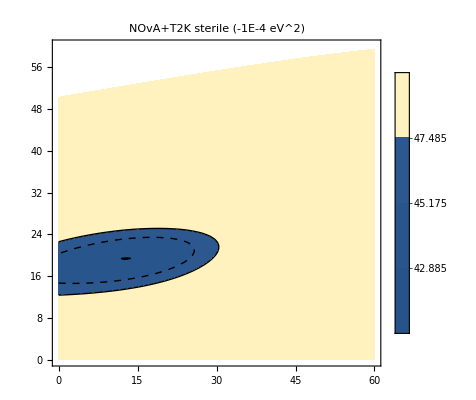

{0.210691,0.140461}

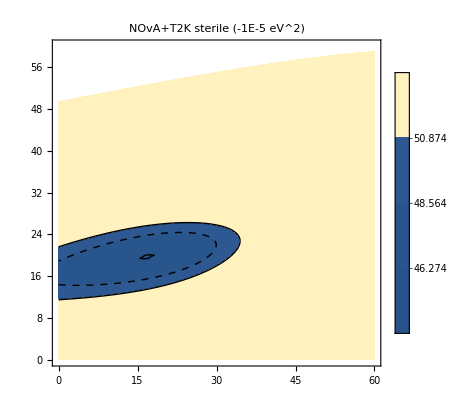

{0.217075,0.191537}

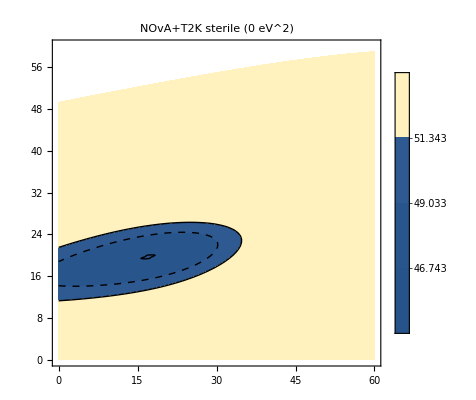

{0.210691,0.178768}

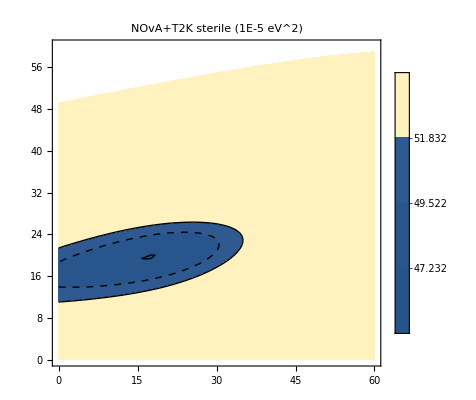

{0.210691,0.185152}

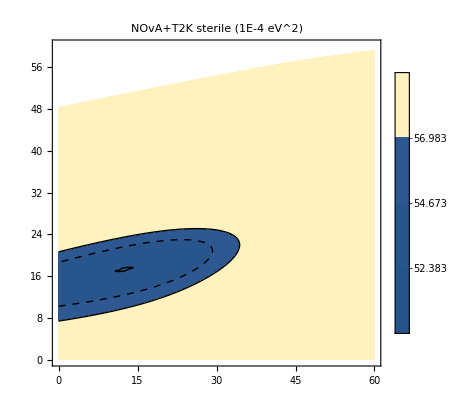

{0.191537,0.146845}

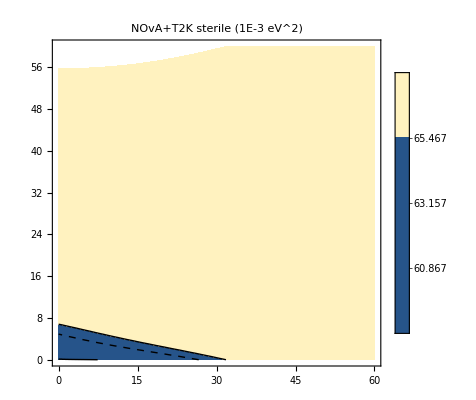

{0.00638457,0.0383074}

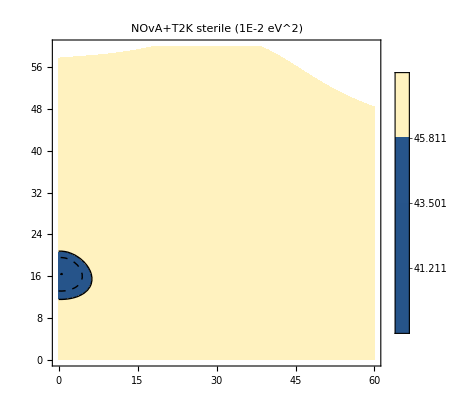

{0.178768,0.0127691}

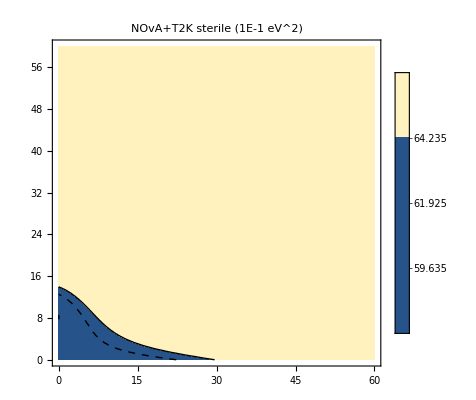

{0.089384,0.00638457}

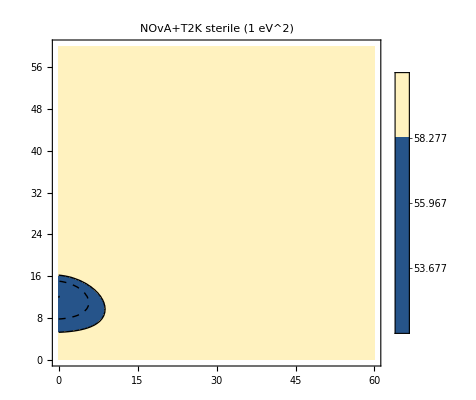

{0.134076,0.00638457}

```mathematica
ρ=2.8;LT2K=N[295];LNOvA=N[810];

dm21=7.42*^-5;dm31=2.41*^-3; dm41=-1*^-4;

θ12=33.44 Degree; θ13=8.57 Degree; θ23=49.0 Degree;
δ13=N[195 Degree];
θ34=0.0;δ34=0.0;δ14=0.0 Degree;

θ24=Range[ArcSin[Sqrt[0.0]],ArcSin[Sqrt[20.0 Degree]],(ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99];
θ14=N[Range[ArcSin[Sqrt[0.0]],ArcSin[Sqrt[20.0 Degree]],(ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99]];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (-1E-4 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}


dm41=N[-1*^-5];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (-1E-5 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}


dm41=N[0];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (0 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}


dm41=N[1*^-5];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (1E-5 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}


dm41=N[1*^-4];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (1E-4 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}


dm41=N[1*^-3];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (1E-3 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}



dm41=N[1*^-2];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (1E-2 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}



dm41=N[1*^-1];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (1E-1 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}


dm41=N[1];

T2KμGrid=ParallelTable[P[2,2,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Kμ=T2KμGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Kμ=Sum[(CountGridT2Kμ[[n]]-FDT2Kμ[[n]])^2/FDT2Kμ[[n]],{n,1,Length[FDT2Kμ]}];
CountGridT2Kantiμ=T2KμGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantiμ=Sum[(CountGridT2Kantiμ[[n]]-FDT2Kantiμ[[n]])^2/FDT2Kantiμ[[n]],{n,1,Length[FDT2Kantiμ]}];

T2KeGrid=ParallelTable[P[2,1,ρ,LT2K,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseT2KND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridT2Ke=T2KeGrid[[;;,;;,;;,1]]T2KND[[;;,2]];
XT2Ke=Sum[(CountGridT2Ke[[n]]-FDT2Ke[[n]])^2/FDT2Ke[[n]],{n,1,Length[FDT2Ke]}];
CountGridT2Kantie=T2KeGrid[[;;,;;,;;,2]]antiT2KND[[;;,2]];
XT2Kantie=Sum[(CountGridT2Kantie[[n]]-FDT2Kantie[[n]])^2/FDT2Kantie[[n]],{n,1,Length[FDT2Kantie]}];


NOvAμGrid=ParallelTable[P[2,2,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAμ=NOvAμGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAμ=Sum[(CountGridNOvAμ[[n]]-FDNOvAμ[[n]])^2/FDNOvAμ[[n]],{n,1,Length[FDNOvAμ]}];
CountGridNOvAantiμ=NOvAμGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantiμ=Sum[(CountGridNOvAantiμ[[n]]-FDNOvAantiμ[[n]])^2/FDNOvAantiμ[[n]],{n,1,Length[FDNOvAantiμ]}];

NOvAeGrid=ParallelTable[P[2,1,ρ,LNOvA,K,dm21,dm31,dm41,θ34,δ34,θy,θx,δ14,θ23,θ13,δ13,θ12],{K,baseNOvAND[[;;,1]]},{θy,θ24},{θx,θ14}];

CountGridNOvAe=NOvAeGrid[[;;,;;,;;,1]]NOvAND[[;;,2]];
XNOvAe=Sum[(CountGridNOvAe[[n]]-FDNOvAe[[n]])^2/FDNOvAe[[n]],{n,1,Length[FDNOvAe]}];
CountGridNOvAantie=NOvAeGrid[[;;,;;,;;,2]]antiNOvAND[[;;,2]];
XNOvAantie=Sum[(CountGridNOvAantie[[n]]-FDNOvAantie[[n]])^2/FDNOvAantie[[n]],{n,1,Length[FDNOvAantie]}];

XT2K=XT2Kμ+XT2Kantiμ+XT2Ke+XT2Kantie;XNOvA=XNOvAμ+XNOvAantiμ+XNOvAe+XNOvAantie;

ListContourPlot[XNOvA+XT2K,DataRange->{{0.,60},{0,60}},Contours->{{Min[XNOvA+XT2K]+0.01,Thick},{Min[XNOvA+XT2K]+2.3,Dashed},{Min[XNOvA+XT2K]+4.61,Thick}},PlotLegends->Automatic,PlotLabel->"NOvA+T2K sterile (1 eV^2)"]
xpos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,1]];
ypos=Position[XNOvA+XT2K,Min[XNOvA+XT2K]][[1,2]];
{N[xpos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)],
N[ypos*((ArcSin[Sqrt[20.0 Degree]]-ArcSin[Sqrt[0.0]])/99)]}
```